```mathematica
1.
f[x_] = (x^5 - 2 x^2 + 3 x + 4)/ (x^5 - 2 x -1)
```

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

```mathematica
f[1]
```

-3

```mathematica
f[2]
```

34/27

```mathematica
f[3]
```

119/118

```mathematica
f[4]
```

144/145

```mathematica
ReplaceAll
```

```mathematica
(x^5 - 2 x^2 + 3 x + 4)/ (x^5 - 2 x -1)/. x-> 1
```

-3

```mathematica
Table[(x^5 - 2 x^2 + 3 x + 4)/ (x^5 - 2 x -1), {x, 10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

```mathematica
2.
Sez = Table[x, {x, 10, 70, 10}]
```

{10,20,30,40,50,60,70}

```mathematica
Take[Sez, 3]
```

{10,20,30}

```mathematica
Take[Sez, -2]
```

{60,70}

```mathematica
Take[Sez, {2, 4}]
```

{20,30,40}

```mathematica
Part[Sez, {2, 3, 5}]
```

{20,30,50}

```mathematica
Drop[Sez, {4, 5}]
```

{10,20,30,60,70}

```mathematica
3.
```

```mathematica
sez = {x^6, x^2, a}
```

{x^6,x^2,a}

```mathematica
sez/. x -> 3
```

{729,9,a}

```mathematica
sez/. x -> x^2
```

{x^12,x^4,a}

```mathematica
sez/. x -> x^(1/2)
```

{x^3,x,a}

```mathematica
sez /. x -> {1, 2, 3}
```

{{1,64,729},{1,4,9},a}

```mathematica
sez/. {x -> 3,  a -> x}
```

{729,9,x}

```mathematica
ReplaceRepeated
```

```mathematica
sez//. {x -> 3,  a -> x}
```

{729,9,3}

```mathematica
sezsez = {sez /. x -> 1,sez /. x -> 2, sez /. x -> 3}
```

{{1,1,a},{64,4,a},{729,9,a}}

```mathematica
4.
```

```mathematica
f[x_] = x^5 + 4 x^3 - 9
```

-9+4 x^3+x^5

```mathematica
odvod = f'[x]
```

12 x^2+5 x^4

```mathematica
odvod /. x -> {1,5}
```

{17,3425}

```mathematica
g[x_]  = ⅇ^(x^(1/4))
```

ⅇ^(x^(1/4))

```mathematica
odvod = g'[x]
```

(ⅇ^(x^(1/4)))/(4 x^(3/4))

```mathematica
odvod /. x -> {1, 2}
```

{ⅇ/4,(ⅇ^(2^(1/4)))/(4 2^(3/4))}

```mathematica
f[x_] = RealAbs[x + 1]
```

RealAbs[1+x]

```mathematica
odvod = f'[x]
```

(1+x)/RealAbs[1+x]

```mathematica
odvod/. x -> {1, -1}
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{1,Indeterminate}

```mathematica
g[x_] = a x^2 + 3 b
```

3 b+a x^2

```mathematica
odvod = g'[x]
```

2 a x

```mathematica
odvod/. x-> {1, 2}
```

{2 a,4 a}

```mathematica
5.
```

```mathematica
f[x_] = x^3 Log[4x + 5]
```

x^3 Log[5+4 x]

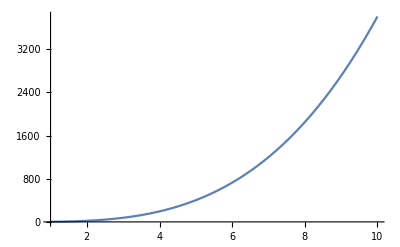

```mathematica
Plot[f[x], {x, 1, 10}]
```

```mathematica
f[x] /. x -> 5
```

125 Log[25]

```mathematica
k = f'[x]
```

(4 x^3)/(5+4 x)+3 x^2 Log[5+4 x]

```mathematica
k = k /. x -> 5
```

20+75 Log[25]